```mathematica
Enter the Mathematica  package that generates an autoregressive price sequence.
```

```mathematica
<<C:\Users\jeoku\OneDrive\Documents\chapman\CS533\programs\SizePower.m
```

```mathematica
(*  MANY OF THE CALCULATIONS IN THIS NOTEBOOK RUN MUCH FASTER    *)
(*  WITH MORE THAN ONE PROCESSOR.  IF YOUR MACHINE HAS MULTIPLE  *)
(*  PROCESSORS YOU CAN ACCESS THEM BY GOING TO "Evaluation" IN   *)
(*  THE MENU ABOVE AND SCROLLING DOWN TO "Parallel Kernel        *)(*  Status ...".  THEN CLICK THE "Launch All" BUTTON.            *)
```

```mathematica
(*  The syntax for linear regression in Mathematica is a bit     *)
(*  unusual.  If data are generated by the equation              *)
(*  g[x] = 3 x + 2 then the data are represented, for example,   *)
(*  as d = {{1, 5}, {2, 8}, {3, 11}}.  Then                     *)
 (*  LinearModelFit[{{1, 5}, {2, 8}, {3, 11}}, {1, x}, x]       *)(*  will return the correct function.                            *)
```

```mathematica
LinearModelFit[{{1, 5}, {2, 8}, {3, 11}}, {1, x}, x]
```

FittedModel[2.+3. x]

```mathematica
FittedModel[2.+3. x]
```

FittedModel[2.+3. x]

```mathematica
(*  The next function shows a simulation and reports intermediate   *)
(*  calculations from the function bEsttStatLinear.  This is a      *)
(*  a traditional linear regression with independent errors.        *)
(*  We'll use this as a baseline for interpretation of time         *)
(*  series with serial correlation.                                 *)
```

```mathematica
bEsttStatLinearTest[3, 0.3, 40, 1]
```

{{3.0038,3.67665,5.52762,4.10147,3.12485,3.80788,6.08618,3.36655,6.178,5.76299,7.73371,5.10842,5.41551,7.74873,7.44318,8.76058,8.71214,8.14901,10.3092,9.50955,10.0198,8.08237,9.71036,10.3041,11.7575,12.003,9.56825,12.814,10.9694,10.8867,11.153,12.3466,12.0148,14.8573,13.7269,14.8759,12.7479,14.7143,14.8043,14.7039},FittedModel[2.94926+0.30197 x], | Estimate | Standard Error | t-Statistic | P-Value
1 | 2.94926 | 0.339405 | 8.68951 | 1.45484×10^-10
x | 0.30197 | 0.0144265 | 20.9317 | 1.84207×10^-22,0.30197,0.0144265,20.9317}

```mathematica
(*  The function bEsttStatLinear[a, b, n, σ] generates a sequence of      *)
(*  length 'n' with intercept 'a' and slope 'b'.  The equation is         *)
(*  y[x] = a + b * x + e[t].  The function returns triples (b̂, t, p)     *)
(*  where b̂ is the estimate the linear coefficient, t is the t-statistic  *)
(*  associated with the estimate and p is the p-value associated with     *)
(*  the estimate.                                                         *)
```

{-0.000889651,-0.0642332,0.949121}

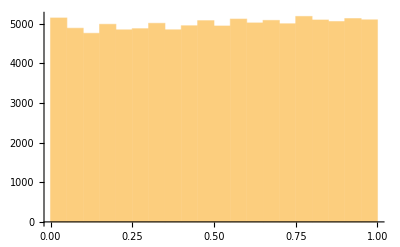

```mathematica
bEsttStatLinear[3, 0, 40, 1]
```

```mathematica
(*  We typically get good estimates of the slope and intercept   *)
(*  that generated the data even with small sample sizes.  The   *)
(*  next simulation shows that with a sample of size n = 40 we   *)
(*  often get estimates of the intercept and slope that are      *)
(*  close to the values of the model that generate the data.     *)
(*  Data in these simulations are generated according to the     *)
(*  equation y[x] = a + b * x + e[t].                           *)
```

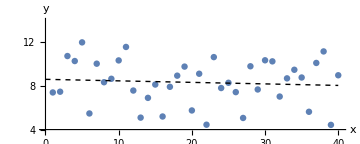
{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 8.61186 | 0.666468 | 12.9217 | 1.75828×10^-15
x | -0.0139705 | 0.0283283 | -0.493163 | 0.624735,-Graphics-}

```mathematica
bEsttStatLinearGraph[8, 0, 40, 2]
```

```mathematica
(*  The next function carries out a large number of simulations.  *)
(*  The data from each simulation is estimated by a linear model  *)
(*  (which is the same model that generated the data).  As we     *)
(*  saw two steps back in this notebook, from each estimation     *)
 (*  the function returns the estimate of the adjustment rate      *)
(*  and a t-statistic.                                            *)
```

```mathematica
btpN100b0L1000k = ParallelTable[bEsttStatLinear[3, 0, 100, 1], {1000000}];
```

```mathematica
(*  The vector btpN100b0L1000k is a vector of 1 million triples.   *)
(*  As described previously (in the discussion of the output       *)
(*  of bEsttStatLinear[a, b, n, σ] each triple has an estimate     *)
(*  of the slope b, a t-statistic for that estimate and a p-value  *)
(*  for whether the estimate differs from zero.  The operation     *)
(*  Transpose[btpN100b0L1000k] collects all of the slope           *)
(*  estimates in one vector, the t-statistics in a second vector   *)
(*  and the p-values in a third vector.  The slope estimates are   *)(*  in the next operation (Transpose[btpN100b0L1000k][[1]]).      *) 
(*  The next function produces a histogram of those estimates.     *)
```

```mathematica
bSort = Sort[Transpose[btpN100b0L1000k][[1]]];
```

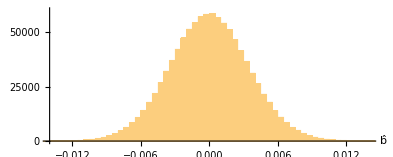

```mathematica
Histogram[bSort, 56, AxesOrigin -> {-0.014, 0}, 
                    PlotRange -> {{-0.014, 0.014}, {0, 60000}}, 
                    AspectRatio -> 0.4, AxesLabel -> {OverHat["b"], ""}]
```

```mathematica
(*  The next calculation tells us that estimates are unbiased.  *)
```

```mathematica
Mean[bSort]
```

-1.48575×10^-6

```mathematica
(*  The next calculations are used to make a histogram of the   *)
(*  t-statistics from the slope estimates and to establish      *)
(*  critical values for tests of the hypothesis that the        *)
(*  slope coefficients are positive.                            *)
```

```mathematica
tSort = Sort[Transpose[btpN100b0L1000k][[2]]];
```

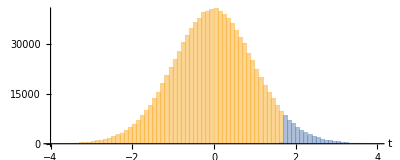

```mathematica
Histogram[{Take[tSort, {1, 953000}],Take[tSort, {953001, 1000000}]},80, AxesOrigin -> {-4, 0}, PlotRange -> {{-4, 4}, {0,40000}}, AspectRatio -> 0.4, AxesLabel -> {"t", ""}]
```

```mathematica
{tSort[[950000]], tSort[[990000]], tSort[[995000]]}
```

{1.66503,2.41977,2.71032}

```mathematica
(*                    HOMEWORK PROBLEM 2                     *)
(*  When we estimate slope coefficients on data that is      *)
(*  generated by a linear model with slope zero and look     *)
(*  at t-statistics from those slope coefficients we find    *)
(*  a value for the t-statistics that is in the upper tail   *)
(*  of the distribution.  Those are the ones that            *)
(*  statistically have the appearance of having been         *)
(*  generated by the linear model with a positive slope      *)(*  (even though they were generated by a model with zero    *)
(*  slope).                                                  *)
(*                                                           *)
(*  Figure 13 in the lecture notes shows a distribution of   *)
(*  t-statistics from the linear model with zero slope.      *)
(*  The simulations that were used to create figure 13       *)
(*  in the lecture notes had length 100.                     *)
(*                                                           *)
(*  Generate a new distribution and graph like the one in    *)
(*  figure 13 and find the 95th and 99th percentiles of      *)
(*  the distribution using sequences of length 40.           *)
```

```mathematica
(*  THIS IS THE END OF HOMEWORK PROBLEM 2.                   *)
```

```mathematica
(*  How do we interpret the t-statistics?  In this next           *)(*  calculation the standard deviation of the error terms         *)(*  is quadrupled relative to the previous calculation.           *)
```

```mathematica
btn100b0s4 = ParallelTable[bEsttStatLinear[3,0,100,4], {i, 1, 100000}];
```

```mathematica
bEstn100b0s4= Sort[Transpose[btn100b0s4][[1]]];
```

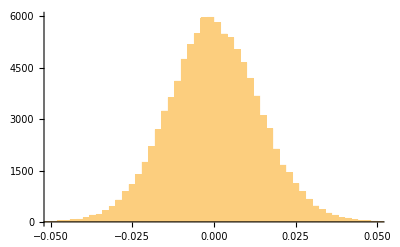

```mathematica
s4Hist = Histogram[bEstn100b0s4, 50, PlotRange -> {{-0.05, 0.05}, {0, 6000}}]
```

```mathematica
btn100b0s1= ParallelTable[bEsttStatLinear[3,0,100,1], {i, 1, 100000}];
```

```mathematica
bEstn100b0s1= Sort[Transpose[btn100b0s1][[1]]];
```

```mathematica
(*  We see that the estimates of' b' have a range that is      *)
(*  four times as big when the error term standard deviation   *)
(*  is quadrupled.                                             *)
```

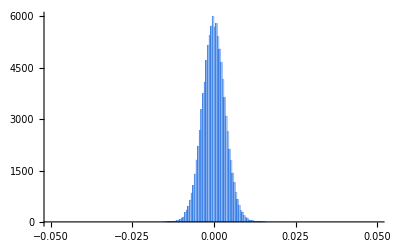

```mathematica
s1Hist = Histogram[bEstn100b0s1, 50,ChartElementFunction->"FadingRectangle",ChartStyle->Hue[0.6, 0.8, 0.9, 0.7], PlotRange -> {{-0.05, 0.05}, {0, 6000}}]
```

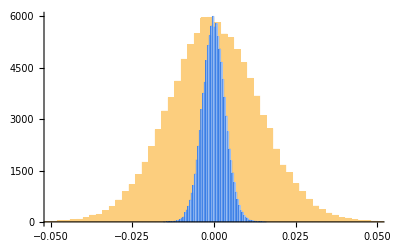

```mathematica
Show[{s4Hist, s1Hist}]
```

```mathematica
tStatn100b0s1= Sort[Transpose[btn100b0s1][[2]]];
```

```mathematica
tStatn100b0s4= Sort[Transpose[btn100b0s4][[2]]];
```

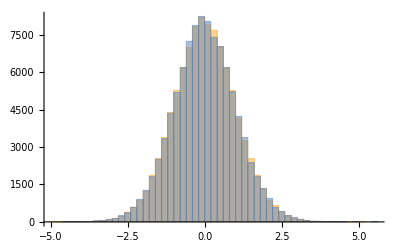

```mathematica
Histogram[{tStatn100b0s1, tStatn100b0s4}, 50]
```

```mathematica
(*  But we also see that the t-statistics are no different.   *)
(*  There are more large estimates of the slope (both         *)
(*  positive and negative) but the chance that we will        *)(*  Conclude that a slope is significantly different from     *)(*  zero is unchanged.                                        *)
```

```mathematica
{tStatn100b0s1[[95000]], tStatn100b0s1[[99000]]}
```

{1.67596,2.42064}

```mathematica
{tStatn100b0s4[[95000]], tStatn100b0s4[[99000]]}
```

{1.67188,2.43284}

```mathematica
(*  The p-values of an estimate tell us how often            *)
(*  t-statistics for the slope estimate are greater than     *)
(*  a particular t-statistic that we observe.  We should     *)
(*  get a p-value less than 0.05 exactly 5% of the time      *)
(*  when the data are generated under the null hypothesis    *)
(*  of a zero slope term.  Also, under the null hypothesis   *)
(*  of no slope we should get a p-value less than 0.50       *)
(*  exactly 50% of the time.  The distribution of p-values   *)
(*  should be uniform on [0, 1] when data are generated      *)
(*  under the null hypothesis of zero slope.  The next       *)(*  calculation shows that with our simulations that have    *)
(*  slope zero the result is almost uniform.                 *)
```

```mathematica
pSort = Sort[Transpose[btpN100b0L1000k][[3]]];
```

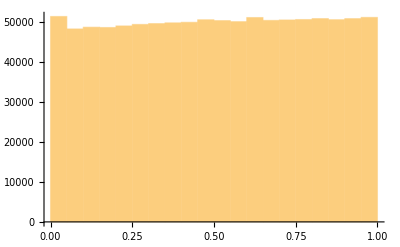

```mathematica
Histogram[pSort]
```

```mathematica
(*  THIS IS THE END OF THE ANALYSIS OF THE LINEAR MODEL   *)
(*  WITH INDEPENDENT ERRORS IN THIS NOTEBOOK.  NOW WE     *)
(*  TURN OUR ATTENTION TO THE AUTOREGRESSIVE MODEL.       *)
```

```mathematica
(*  The function PriceSequenceGraph[c, p0, p*, n, σ] displays   *)
(*  a sequence of length 'n' that is autoregressive with the    *)
(*  form p[t+1] = p[t] + c *(p* - p[t]) + e[t].  The          *)
(*  adjustment rate is 'c', the initial price is p0 and the     *)
(*  central tendancy is p*.  The dashed line in the graph       *)
(*  shows the level p* that the function reverts to if c > 0.   *)
(*  The random terms are independent and identically            *)
(*  distributed normal random variables with a mean of 0        *)
(*  and variance σ^2.                                           *)
```

```mathematica
PriceSequenceGraph[0.0, 30, 20, 500, 1]
```

PriceSequenceGraph[0.,30,20,500,1]

```mathematica
(*  The function cEsttStat[c, p0, p*, n, σ, const] generates  *)
(*  an autoregressive sequence of length' n' with adjustment  *)
(*  rate 'c' starting from the initial value p0.  The         *)
(*  adjustment equation is                                    *)
(*             p[t+1] = p[t] + c(p* - p[t]) + e[t].         *)  
(*  If the option const = 1 is selected then the model        *)
(*                Dp[t+1] = α0 + α1 p[t] + e[t]              *)
(*  is estimated.  If const = 0 is selected then the model    *)
(*                  Dp[t+1] = α1 p[t] + e[t]                 *)
(*  is estimated.  The function returns a triple of values    *)
(*  (ĉ, t, p* ) where ĉ is the estimate of c from the        *)
(*  regression and t is the t-statistic associated with       *) 
(*  the estimate.                                             *)
```

```mathematica
(*  The next function shows a simulation and reports          *)
(*  intermediate calculations from the function cEsttStat.    *)
```

```mathematica
cEsttStatTest2[0.02, 30, 20, 500,1, 1]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.511946 | 0.195951 | 2.61262 | 0.00925724
x | 0.0259606 | 0.00941881 | 2.75625 | 0.00606167,0.0259606,2.75625,2.75625,19.7201}

```mathematica
(*  The function cEsttStatGraph[c, p0, p*, n, σ, const]      *)
(*  adds a graph of the data to the output of the previous   *)
(*  function.                                                *)
```

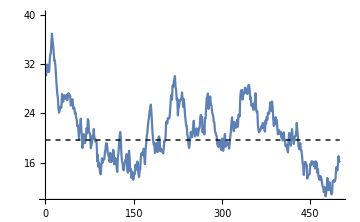
{0.0246289,2.64568,19.6568,-Graphics-}

```mathematica
cEsttStatGraph[0.02, 30, 20, 500, 1, 1]
```

```mathematica
(*  Generate six hundred thousand paths of length 500 and then     *)
(*  calculate the critical value for test statistics of size       *)
(*  0.05 and 0.01.  Under the null hypothesis of no adjustment     *)
(*  the t-statistic will be larger than 2.90 about 5 percent of    *)
(*  the time and larger than 3.50 about 1 percent of the time      *)(*  when the model with a constant is estimated.                   *)
```

```mathematica
ctn500a0L600k = ParallelTable[cEsttStat[0.0, 0, 0, 600, 0.5, 1],
{i, 1, 10000}];
```

```mathematica
tStat500a0L600k= Sort[Transpose[ctn500a0L600k][[2]]];
```

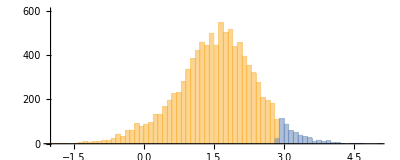

```mathematica
Histogram[{Take[tStat500a0L600k, 9500],Take[tStat500a0L600k, -500]}, 70, AxesOrigin -> {-2, 0}, PlotRange -> {{-2., 5}, {0, 600}}, AspectRatio -> 0.4]
```

```mathematica
{{tStat500a0L600k[[9500]]}, {□}}
```

```mathematica
{{2.884193582395737},{□}}
```

```mathematica
{{tStat500a0L600k[[9518]]}, {□}}
```

{{2.89517},{□}}

```mathematica
(*                    HOMEWORK PROBLEM 3                     *)
(*  When we estimate slope coefficients on data that is      *)
(*  generated by a random walk and look at t-statistics      *)
(*  from those slope coefficients we find a value for        *)
(*  the t-statistics that is in the upper tail of the        *)
(*  distribution.  Those are the ones that statistically     *)
(*  have the appearance of having been generated by the      *)
(*  autoregressive model with a positive adjustment rate     *)(*  (even though they were generated as random walks).       *)
(*                                                           *)
(*  Figure 16 in the lecture notes shows a distribution      *)
(*  of t-statistics for random walks.  The simulations       *)
(*  that were used to create figure 16 in the lecture        *)
(*  notes had length 500.                                    *)
(*                                                           *)
(*  Generate a new distribution and graph like the one in    *)
(*  figure 16 and find the 95th and 99th percentiles of      *)
(*  the distribution using sequences of shorter length.      *)
(*  Choose a length between 100 and 400 in an increment of   *)
(*  100.  (That is, choose sequences of length 100 or 200    *)
(*  or 300 or 400.  The reason I'm asking you to do this     *)
(*  is so that we can compare the results from different     *)
(*  length sequences.)                                       *)
```

```mathematica
(*  THE NEXT THREE FUNCTIONS ARE INCLUDED TO HELP YOU GET    *)
(*  A START ON HOMEWORK PROBLEM 3.                           *)
```

```mathematica
ctn300a0L100k = ParallelTable[cEsttStat[0.0, 0, 0, 300, 0.5, 1],
{i, 1, 100000}];
```

```mathematica
(*  The estimates ĉ are pulled out of this calculation in    *)
(*  the next function.                                       *)
```

```mathematica
cEstn300a0L100k= Sort[Transpose[ctn300a0L100k][[1]]];
```

```mathematica
(*  This is a histogram of the estimates ĉ.  Recall that     *)
(*  we have generated our data under the null hypothesis     *)
(*  of no adjustment.  Even so the estimates ĉ are almost    *)
(*  all greater than 0.                                      *)
```

```mathematica
Histogram[cEstn300a0L100k, 140, AxesOrigin -> {-0.05, 0}, PlotRange -> {{-0.05, 0.30}, {0, 40000}}, AspectRatio -> 0.4, ImageSize -> Medium]
```

```mathematica
(*  NOW WE RETURN TO THE ANALYSIS OF THE SEQUENCES WITH      *)
(*  LENGTH 500 THAT PRECEEDED HOMEWORK PROBLEM 3.            *)
```

```mathematica
(*  The mean estimate ĉ is greater than zero.                *)
```

```mathematica
cStat500a0L600k= Sort[Transpose[ctn500a0L600k][[1]]];
```

```mathematica
{Mean[cStat500a0L600k], Median[cStat500a0L600k]}
```

{0.0108271,0.00875119}

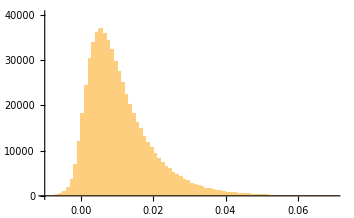

```mathematica
Histogram[cStat500a0L600k, 100, AxesOrigin -> {-0.01, 0}, PlotRange -> {{-0.01, 0.07}, {0, 40000}}]
```

```mathematica
(*  What if we have a positive adjustment rate?  What will    *)
(*  the distribution of estimates be for the adjustment rate  *)
(*  and what will be the distribution of t-statistics?        *)
(*  This simulation uses a positive adjustment rate to        *)
(*  examine these questions.                                  *)
```

```mathematica
ctn500a02L100k = ParallelTable[cEsttStat[0.02, 20, 20, 500, 0.5, 1],
{i, 1, 100000}];
```

```mathematica
Map[Mean, Transpose[ctn500a02L100k]]
```

{0.029433,2.6152,0.607163}

```mathematica
tStat500a02L100k= Sort[Transpose[ctn500a02L100k][[2]]];
```

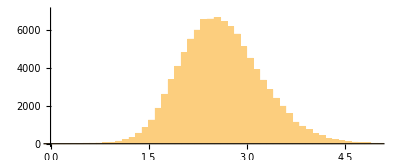

```mathematica
Histogram[tStat500a02L100k, 50, AxesOrigin -> {0, 0}, PlotRange -> {{0, 5}, {0, 7000}}, AspectRatio -> 0.4]
```

```mathematica
(*  The next calulation determines how many of the t-statistics   *)
(*  are below the critical value of 2.90.                         *)
```

```mathematica
Length[Position[Map[Sign, tStat500a02L100k - 2.90], -1]]
```

69730

```mathematica
(*  We just completed our first calculation of the power of a     *)
(*  test.  We now know that with sequences of length n = 500      *)
(*  and an adjustment rate of c = 0.02 above 30.4% of the         *)
(*  t-statistics are above the 5% critical value.  That means     *)
(*  that when adjustment is present, we are able to detect it     *)(*  approximately 30.4% of the time.                              *)
```

```mathematica
<<D:\\Economics\Courses\MGSC533\2021\Data\BRLpCADpGBPpJPYpMXNpNOKpTRLpUSD.txt;
```

```mathematica
{Length[NOKpUSD], Length[USDpGBP]}
```

{600,600}

#### We now know how to interpret the results of the movement between the pound and dollar since the float began in 1971.

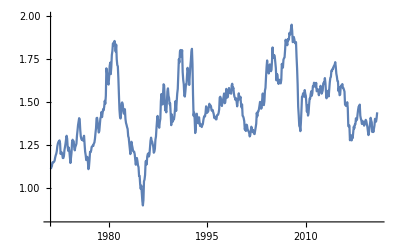

```mathematica
ListPlot[USDpGBP, Joined -> True, AxesOrigin -> {1971, 0.8}, PlotRange-> {{1971, 2021}, {0.8, 2.0}}]
```

```mathematica
(*  The function cEsttStat returns an estimate of the    *)
(*  adjustment rate 'c', the t-statistic associated      *)
(*  with that adjustment rate, and the estimate of the   *) (*  level  that the series fluctuates around. For the    *)
(*  most part as the exchange rate sequence gets longer  *)
(*  it looks (statistically) more like it is fluctuating *)
(*  around some level.  We can see this from the         *)
(*  t-statistics which are the second element in the     *)
(*  output of cEsttStat[]. These t-statistics are        *)
(*  getting closer to the 5% critical value of 2.89.     *)
```

```mathematica
cEsttStat[Take[Transpose[USDpGBP][[2]], 516],1]
```

{0.0178698,2.25982,1.51912}

```mathematica
cEsttStat[Take[Transpose[USDpGBP][[2]], 528],1]
```

{0.0181247,2.34782,1.51553}

```mathematica
cEsttStat[Take[Transpose[USDpGBP][[2]], 540],1]
```

{0.0185918,2.43045,1.50969}

```mathematica
cEsttStat[Take[Transpose[USDpGBP][[2]], 552],1]
```

{0.0187344,2.43544,1.4828}

```mathematica
cEsttStat[Take[Transpose[USDpGBP][[2]], 564],1]
```

{0.019231,2.52689,1.49073}

```mathematica
cEsttStat[Take[Transpose[USDpGBP][[2]], 576],1]
```

{0.0191445,2.53211,1.48332}

```mathematica
cEsttStat[Take[Transpose[USDpGBP][[2]], 588],1]
```

{0.0192727,2.57476,1.48471}

```mathematica
cEsttStat[Take[Transpose[USDpGBP][[2]],600],1]
```

{0.0193909,2.60874,1.48504}

#### With data through December 2020 we still cannot conclude that the dollar - pound exchange rate series starting in 1971 is mean reverting.

```mathematica
(*  The last calculation above gives us a t-statistic for     *)
(*  mean reversion of the dollar-pound exchange rate through  *)
(*  the December 2020.  We get a t-statistic of 2.60874 for   *) (*  this series.  What is the p-value associated with this    *)(*  t-statistic?                                              *)
```

```mathematica
(*  The next 5 calculations repeat the calculation of the 'c'     *)
(*  estimate, t-statistic, and the exchange rate 'attractor'      *) (*  that we did above for the dollar-pound exchange rate for      *)(*  5 other exchange rates.  Use these for the rest of the        *)(*  homework problem on p-values for mean reversion of the        *)
(*  exchange rates.                                               *)
```

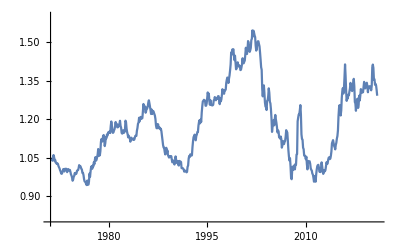

```mathematica
ListPlot[CADpUSD, Joined -> True, AxesOrigin -> {1971, 0.8}, PlotRange-> {{1971, 2021}, {0.8, 1.6}}]
```

```mathematica
cEsttStat[Take[Transpose[CADpUSD][[2]], 600],1]
```

{0.00732321,1.48382,1.22679}

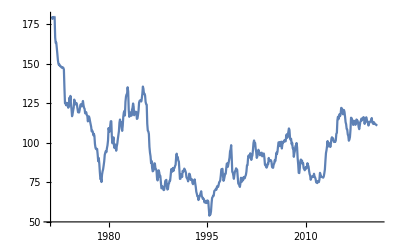

```mathematica
ListPlot[JPYpUSD, Joined -> True, AxesOrigin -> {1971, 50}, PlotRange-> {{1971, 2021}, {50, 180}}]
```

```mathematica
cEsttStat[Take[Transpose[JPYpUSD][[2]], 600],1]
```

{0.0176129,3.72547,91.8239}

```mathematica
cEsttStat[Take[Transpose[NOKpUSD][[2]], 600],1]
```

{0.0100678,1.5779,7.15559}

```mathematica
cEsttStat[Take[Transpose[JPYpGBP][[2]], 600],1]
```

{0.0147181,2.39535,130.784}

```mathematica
(*  I HAVE NOT COVERED THE MATERIAL BELOW DURING LECTURES.   *)
(*  I DON'T PLAN TO COVER THIS MATERIAL AND I WON'T GIVE     *)
(*  A HOMEWORK ASSIGNMENT ON IT.  I THINK IT IS USEFUL       *)
(*  THOUGH SO I AM LEAVING IT IN THE NOTEBOOK.               *)
```

#### A classical test for a significant parameter would use a t -test and the critical value for the test statistic would be 1.660 for a sample size of 100. See the value in the table under the column with 1 - α = 0.95 and the row with ν = 100 in the table at http : // www.itl.nist.gov/div898/handbook/eda/section3/eda3672.htm.

#### If we subtract 1.66 from each element of tStat then all of the t - statistics that are below the (inappropriate) critical value of 1.66 will be less than 0 and all those that are greater than the critical value will be positive. Then we can take the sign of the result to distinguish the t - statistics below 1.66 from the ones above. All the ones above 1.66 would lead to acceptance of the null hypothesis of adjustment (which is inappropriate in this case). We can count those up by taking Length[Position[Map[Sign, tStat - 1.66], 1]. Those are all of the cases where we incorrectly conclude that there is adjustment. The result is distorted so this critical value is not appropriate.

```mathematica
ctn100a0const0 = ParallelTable[cEsttStat[0.0, 0, 0, 100, 0.5, 0],{i, 1, 100000}];
```

```mathematica
cEst100const0= Sort[Transpose[ctn100a0const0][[1]]];
```

```mathematica
Mean[cEst100const0]
```

0.0177346

```mathematica
tStat100a0const0 = Sort[Transpose[ctn100a0const0][[2]]];
```

```mathematica
{tStat100a0const0[[95000]],tStat100a0const0[[99000]]}
```

{1.95224,2.5866}

```mathematica
N[1 - Flatten[Position[Map[Sign, tStat100a0const0 - 1.66], -1]][[-1]]/100000]
```

0.0931

```mathematica
The previous calculation shows that about 9.4% of the observed t-statistics are above 1.660 rather than the 5% that we would get if the errors were independent and identically distributed.
```

```mathematica
When the model with a constant is estimated the t statistic will be larger than 2.90 about 5 percent of the time and larger than 3.50 about 1 percent of the time .
```

```mathematica
ctn100a0const1 = ParallelTable[cEsttStat[0.01, 0, 0, 100, 0.5, 1], {i, 1, 100000}];
```

```mathematica
tStatn100const1 = Sort[Transpose[ctn100a0const1][[2]]];
```

```mathematica
{tStatn100const1[[95000]], tStatn100const1[[99000]]}
```

{2.90668,3.51452}

```mathematica
cEstn100const1 = Sort[Transpose[ctn100a0const1][[1]]];
```

```mathematica
Mean[cEstn100const1]
```

0.0534495

```mathematica
ctn100a0const1 = ParallelTable[cEsttStat[0.01, 0, 0, 552, 0.5, 0], {i, 1, 100000}];
```

```mathematica
cEstn100const1 = Sort[Transpose[ctn100a0const1][[1]]];
```

```mathematica
Mean[cEstn100const1]
```

0.0137589

```mathematica
ctn100a0const1 = ParallelTable[cEsttStat[0.01, 0, 0, 552, 0.5, 1], {i, 1, 100000}];
```

```mathematica
cEstn100const1 = Sort[Transpose[ctn100a0const1][[1]]];
```

```mathematica
Mean[cEstn100const1]
```

0.0190498

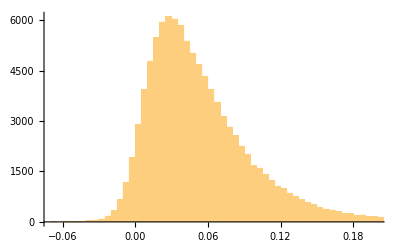

```mathematica
Histogram[cEstn100const1, 100]
```

```mathematica
N[1 - Length[Position[Map[Sign, tStatn100const1 - 1.66], -1]]/Length[tStatn100const1]]
```

0.45702

```mathematica
N[1 - Length[Position[Map[Sign, tStatn100const1 - 2.90], -1]]/Length[tStatn100const1]]
```

0.05085

```mathematica
cEstconst1 = Sort[Transpose[ctn100a0const1][[1]]];
```

```mathematica
Mean[cEstc1]
```

```mathematica
Histogram[cEstc1, 100]
```

#### Why is the estimate ĉ so much higher when a constant is included in the regression and why are the t-statistics so much higher when a constant is included in the regression? This is not an easy question to answer but I'd like you to think about it before I discuss it.

#### When adjustment is present but the adjustment rate is small there is a high probability that the null hypothesis of no adjustment is accepted, even though it is false, i.e., the estimation technique has low power. The examples below find the frequency with which adjustment is rejected even though it is present.The first example shows that with a small adjustment rate of α = 0.02 and a small sample size of n = 100 adjustment is rejected about 90 % of the time.